```mathematica
List1 = {1, 2, 3, 4};
List1[[3]]
```

3

```mathematica
List2 = Table[1. Sin[k], {k,1,30}];
```

```mathematica
%14
```

```mathematica
{0.8414709848078965,0.9092974268256817,0.1411200080598672,-0.7568024953079282,-0.9589242746631385,-0.27941549819892586,0.6569865987187891,0.9893582466233818,0.4121184852417566,-0.5440211108893698,-0.9999902065507035,-0.5365729180004349,0.4201670368266409,0.9906073556948704,0.6502878401571168,-0.2879033166650653,-0.9613974918795568,-0.7509872467716762,0.14987720966295234,0.9129452507276277,0.8366556385360561,-0.008851309290403876,-0.8462204041751706,-0.9055783620066238,-0.13235175009777303,0.7625584504796027,0.956375928404503,0.27090578830786904,-0.6636338842129675,-0.9880316240928618}

List2 = Append[List2, π]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021,-0.99999,-0.536573,0.420167,0.990607,0.650288,-0.287903,-0.961397,-0.750987,0.149877,0.912945,0.836656,-0.00885131,-0.84622,-0.905578,-0.132352,0.762558,0.956376,0.270906,-0.663634,-0.988032}

```mathematica
{0.8414709848078965,0.9092974268256817,0.1411200080598672,-0.7568024953079282,-0.9589242746631385,-0.27941549819892586,0.6569865987187891,0.9893582466233818,0.4121184852417566,-0.5440211108893698,-0.9999902065507035,-0.5365729180004349,0.4201670368266409,0.9906073556948704,0.6502878401571168,-0.2879033166650653,-0.9613974918795568,-0.7509872467716762,0.14987720966295234,0.9129452507276277,0.8366556385360561,-0.008851309290403876,-0.8462204041751706,-0.9055783620066238,-0.13235175009777303,0.7625584504796027,0.956375928404503,0.27090578830786904,-0.6636338842129675,-0.9880316240928618,π}
Length[List2]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021,-0.99999,-0.536573,0.420167,0.990607,0.650288,-0.287903,-0.961397,-0.750987,0.149877,0.912945,0.836656,-0.00885131,-0.84622,-0.905578,-0.132352,0.762558,0.956376,0.270906,-0.663634,-0.988032,π}

31

```mathematica
Formula2 = x^2 - x*y + y^3 - 3;
SubRule4 = {x->4, y->7};
Formula2 /. SubRule4
```

328

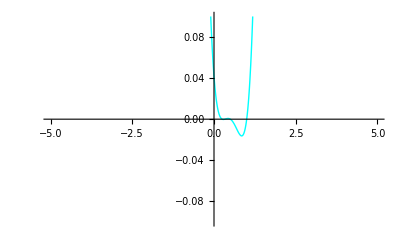

```mathematica
formula = (x-1)(x-1/2)(x-1/3)(x-1/4);
Plot[formula, {x, -5, 5}, PlotRange-> {-.1, .1}, PlotStyle->{Thick, Cyan}]
```